NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

{{α[t]→InterpolatingFunction[…][t],β[t]→InterpolatingFunction[…][t]}}

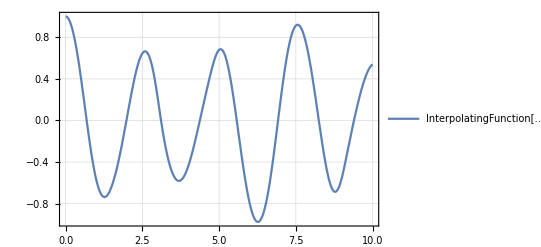

```mathematica
g=9.81;
Subscript[m, OC]=1;
Subscript[J, OC] =1.25;
Subscript[l, OC]=1;
Subscript[k, OC]=0.5;
Subscript[m, CB]=1;
Subscript[J, CB] =1.25;
Subscript[l, CB]=1;
Subscript[k, CB]=0.5;
eqns={
α'[t]==α1[t],
β'[t]==β1[t],
α''[t] Subscript[J, OC]+g Sin[α[t]] Subscript[l, OC] Subscript[m, CB]+α'[t] β'[t] Sin[α[t]-β[t]] Subscript[k, OC] Subscript[l, OC] Subscript[m, CB]+1/2 (2 β''[t] Cos[α[t]-β[t]] Subscript[k, OC] Subscript[l, OC]-2 (α'[t]-β'[t]) β'[t] Sin[α[t]-β[t]] Subscript[k, OC] Subscript[l, OC]+2 α''[t] Subscript[l, OC]^2) Subscript[m, CB]+g Sin[α[t]] Subscript[k, OC] Subscript[m, OC]==0,
g Sin[β[t]] Subscript[k, CB] Subscript[m, CB]-α'[t] β'[t] Sin[α[t]-β[t]] Subscript[k, OC] Subscript[l, OC] Subscript[m, CB]+1/2 (2 β''[t] Subscript[J, CB]+2 α''[t] Cos[α[t]-β[t]] Subscript[k, OC] Subscript[l, OC] Subscript[m, CB]-2 α'[t] (α'[t]-β'[t]) Sin[α[t]-β[t]] Subscript[k, OC] Subscript[l, OC] Subscript[m, CB])==0,
α[0]==1,
α'[0]==0,
β[0]==1,
β'[0]==0

};

sol = NDSolve[eqns,{α[t],β[t]},{t,0,20} ]
Plot[Evaluate[α[t]/.sol],{t,0,10},PlotTheme->"Detailed",PlotRange->All]
```

```mathematica
α''[t] Subscript[J, OC]+g Sin[α[t]] Subscript[l, OC] Subscript[m, CB]+α'[t] β'[t] Sin[α[t]-β[t]] Subscript[k, OC] Subscript[l, OC] Subscript[m, CB]+1/2 (2 β''[t] Cos[α[t]-β[t]] Subscript[k, OC] Subscript[l, OC]-2 (α'[t]-β'[t]) β'[t] Sin[α[t]-β[t]] Subscript[k, OC] Subscript[l, OC]+2 α''[t] Subscript[l, OC]^2) Subscript[m, CB]+g Sin[α[t]] Subscript[k, OC] Subscript[m, OC]
```

```mathematica
g Sin[β[t]] Subscript[k, CB] Subscript[m, CB]-α'[t] β'[t] Sin[α[t]-β[t]] Subscript[k, OC] Subscript[l, OC] Subscript[m, CB]+1/2 (2 β''[t] Subscript[J, CB]+2 α''[t] Cos[α[t]-β[t]] Subscript[k, OC] Subscript[l, OC] Subscript[m, CB]-2 α'[t] (α'[t]-β'[t]) Sin[α[t]-β[t]] Subscript[k, OC] Subscript[l, OC] Subscript[m, CB])
```